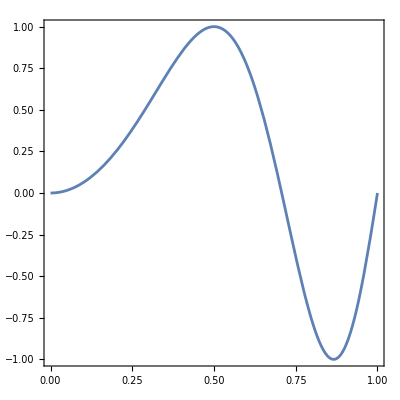

```mathematica
ParametricPlot[{t,Sin[2π t^2]},{t,0,1},Frame->True,PlotRange->All,AspectRatio->1]
```

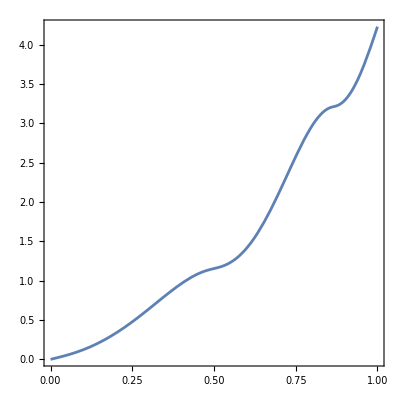

```mathematica
ParametricPlot[{t,ArcLength[Sin[2π x^2],{x,0,t}]},{t,0,1},Frame->True,PlotRange->All,AspectRatio->1]
```

```mathematica
l=N[ArcLength[Sin[2π t^2],{t,0,1}]]
```

4.22891

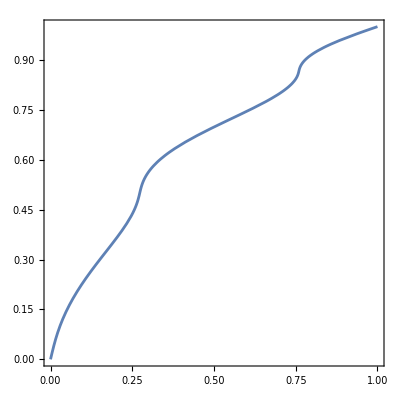

```mathematica
ParametricPlot[{ArcLength[Sin[2π x^2],{x,0,t}]/l,t},{t,0,1},Frame->True,PlotRange->All,AspectRatio->1]
```

```mathematica
lineeq[{{x1_,y1_},{x2_,y2_}},var_]:=FullSimplify[y1+((y2-y1)/(x2-x1))(var-x1)];
```

```mathematica
lineeq[{{1,2},{2,4}},t]
```

2 t

```mathematica
approx[pts_,var_]:=Module[{n,conds,eqs},
n=Length[pts]-1;
conds=Table[pts[[j]][[1]]<=var<=pts[[j+1]][[1]],{j,1,n}];
eqs=Map[lineeq[#,var]&,Table[{pts[[j]],pts[[j+1]]},{j,1,n}]];
Piecewise[Transpose[{eqs,conds}]]
];
```

```mathematica
pts4={{0,0},{0.12486596487113379,0.06868511481948694},{0.5096966711949104,1.100546753343191},{0.5302350641930077,1.1550883912306211},{0.8800206686529878,-1.2037657853746164},{1.0000055404764765,-1.0406736361545654*^-8}};
```

```mathematica
approx[pts4,t]
```

Piecewise[{{0.550071 t, 0≤t≤0.124866}, {-0.266123+2.68134 t, 0.124866≤t≤0.509697}, {-0.253001+2.65559 t, 0.509697≤t≤0.530235}, {4.73084-6.74371 t, 0.530235≤t≤0.880021}, {-10.0327+10.0326 t, 0.880021≤t≤1.00001}, {0, True}}]

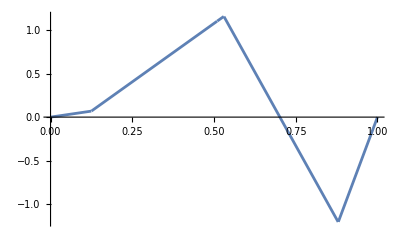

```mathematica
Plot[approx[pts4,t],{t,0,1}]
```

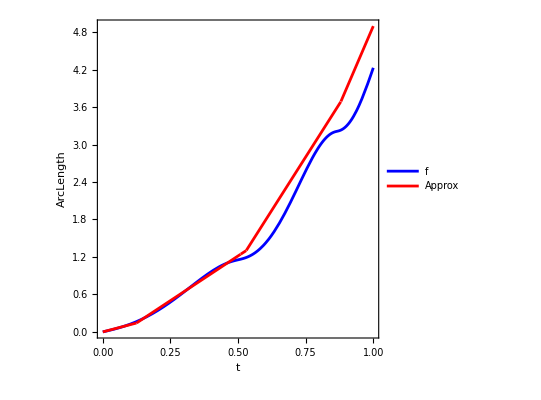

```mathematica
ParametricPlot[{
{t,ArcLength[Sin[2π x^2],{x,0,t}]},
{t,ArcLength[approx[pts4,x],{x,0,t}]}},
{t,0,1},Frame->True,PlotRange->All,AspectRatio->1,
PlotStyle->{Blue,Red},PlotLegends->{"f","Approx"},
FrameLabel->{"t","ArcLength"}]
```

```mathematica
la=N[ArcLength[approx[pts4,t],{t,0,1}]]
```

4.8964

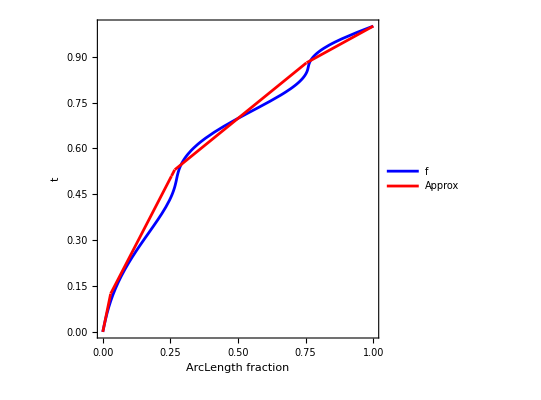

```mathematica
ParametricPlot[
{{ArcLength[Sin[2π x^2],{x,0,t}]/l,t},
{ArcLength[approx[pts4,x],{x,0,t}]/la,t}},
{t,0,1},Frame->True,PlotRange->All,AspectRatio->1,
PlotStyle->{Blue,Red},PlotLegends->{"f","Approx"},
FrameLabel->{"ArcLength fraction","t"}]
```

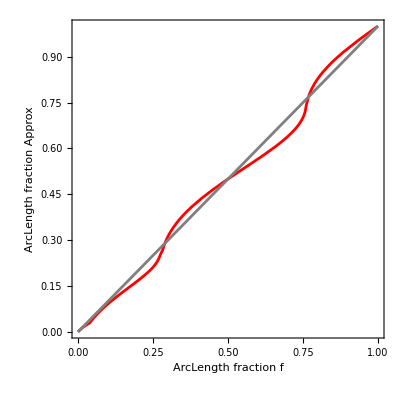

```mathematica
ParametricPlot[
{{ArcLength[Sin[2π x^2],{x,0,t}]/l,ArcLength[approx[pts4,x],{x,0,t}]/la},{t,t}},
{t,0,1},Frame->True,PlotRange->All,AspectRatio->1,
PlotStyle->{Red,Gray},
FrameLabel->{"ArcLength fraction f","ArcLength fraction Approx"}]
```

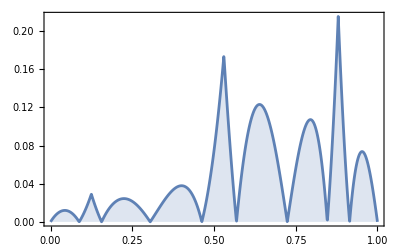

```mathematica
DiscretePlot[EuclideanDistance[{t,Sin[2π t^2]},{t,approx[pts4,t]}],
{t,0,1,10^-3},Frame->True,PlotRange->All]
```

```mathematica
mfdsig4=Mean[Table[EuclideanDistance[{t,Sin[2π t^2]},{t,approx[pts4,t]}],
{t,0,1,10^-3}]]
```

0.0474057

```mathematica
tblrnd[rangex_,rangey_,n_,samples_,first_,last_]:=Map[Prepend[Append[#,last],first]&,Map[Sort,ArrayReshape[Transpose[{RandomReal[rangex,n samples],RandomReal[rangey,n samples]}],{samples,n,2}]]];
```

```mathematica
tblrnd[{0,1},{-2,2},3,10,{0,0},{1,0}]
```

{{{0,0},{0.228823,-0.465141},{0.361479,0.144657},{0.424799,-1.28304},{1,0}},{{0,0},{0.43855,-1.59884},{0.478989,0.167489},{0.917065,-0.688012},{1,0}},{{0,0},{0.140311,1.09664},{0.47989,1.13886},{0.969259,1.65894},{1,0}},{{0,0},{0.272286,-1.06567},{0.72569,0.117593},{0.786236,-0.473515},{1,0}},{{0,0},{0.508549,0.48996},{0.595846,-1.82666},{0.984267,-1.83361},{1,0}},{{0,0},{0.201607,1.36166},{0.492276,-0.846133},{0.725384,-0.629285},{1,0}},{{0,0},{0.00108733,0.243475},{0.760012,-1.16276},{0.78358,0.0253542},{1,0}},{{0,0},{0.174781,-0.137277},{0.827832,1.32938},{0.978822,0.502266},{1,0}},{{0,0},{0.152655,0.618716},{0.473016,0.443058},{0.75298,1.96995},{1,0}},{{0,0},{0.105607,1.23745},{0.402864,-1.27534},{0.539477,-1.14204},{1,0}}}

```mathematica
meandist[f_,pts_,T_,step_]:=Mean[Table[EuclideanDistance[{t,f},{t,approx[pts,t]}],
{t,0,T,step}]];
```

```mathematica
meandist[Sin[2π t^2],pts4,1,10^-3]
```

0.0474057

```mathematica
testtbl=tblrnd[{0,1},{-2,2},3,100,{0,0},{1,0}];
```

```mathematica
genpts[f_,T_,step_,rangex_,rangey_,n_,samples_,first_,last_]:=Module[{tbl},
tbl=tblrnd[rangex,rangey,n,samples,first,last];
SortBy[Map[{#,meandist[f,#,T,step]}&,tbl],Last]];
```

```mathematica
genpts[Sin[2π t^2],1,10^-3,{0,1},{-2,2},3,10,{0,0},{1,0}]
```

{{{{0,0},{0.147754,-0.139198},{0.199738,1.745},{0.977931,-0.997402},{1,0}},0.394319},{{{0,0},{0.614628,0.612849},{0.728469,-1.25721},{0.784009,1.27108},{1,0}},0.552876},{{{0,0},{0.214487,-0.734577},{0.305381,0.64609},{0.680232,-1.28544},{1,0}},0.715686},{{{0,0},{0.619718,-0.0969762},{0.880673,0.404944},{0.985389,1.51691},{1,0}},0.726194},{{{0,0},{0.00669811,-1.13088},{0.304742,0.247673},{0.756446,-1.0988},{1,0}},0.749029},{{{0,0},{0.494383,-0.850355},{0.863254,0.263509},{0.914682,-1.65773},{1,0}},0.840892},{{{0,0},{0.344074,-1.33034},{0.549326,0.184366},{0.637492,0.222994},{1,0}},0.886229},{{{0,0},{0.398925,-1.09905},{0.650744,-0.748244},{0.854408,-1.22717},{1,0}},0.93783},{{{0,0},{0.0394686,-1.51798},{0.686318,-0.385249},{0.708475,-0.129694},{1,0}},1.17485},{{{0,0},{0.0286295,-1.2368},{0.407878,-1.09007},{0.754616,-0.745202},{1,0}},1.21574}}

```mathematica
Timing[testdists=SortBy[Map[{#,meandist[Sin[2π t^2],#,1,10^-3]}&,testtbl],Last];]
```

{3.90811,Null}

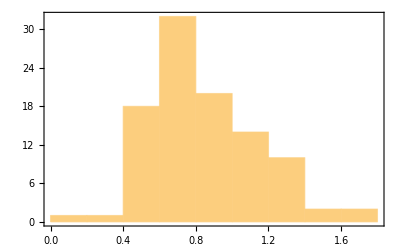

```mathematica
Histogram[Last[Transpose[testdists]],PlotRange->All,Frame->True]
```

```mathematica
Min[Last[Transpose[testdists]]]
```

0.176679

```mathematica
Take[testdists,10]
```

{{{{0,0},{0.428483,0.541832},{0.550594,1.07831},{0.965662,-1.46485},{1,0}},0.176679},{{{0,0},{0.466238,0.551874},{0.635532,1.29968},{0.900084,-0.736322},{1,0}},0.321025},{{{0,0},{0.0116157,-0.675311},{0.646102,0.590891},{0.88356,-1.06707},{1,0}},0.425471},{{{0,0},{0.131529,0.194279},{0.607465,1.40545},{0.767862,0.576229},{1,0}},0.447114},{{{0,0},{0.293655,-0.1499},{0.50605,0.944464},{0.74869,-1.71027},{1,0}},0.469485},{{{0,0},{0.283042,0.187902},{0.914062,0.194417},{0.97919,-1.3443},{1,0}},0.486424},{{{0,0},{0.300654,0.89224},{0.487948,0.930667},{0.653115,-1.48975},{1,0}},0.495588},{{{0,0},{0.1985,1.13487},{0.269125,0.61444},{0.717702,0.345607},{1,0}},0.500295},{{{0,0},{0.201105,-0.999416},{0.610929,1.54981},{0.859825,-1.05293},{1,0}},0.512805},{{{0,0},{0.0461939,-0.248717},{0.523389,0.22224},{0.695094,-0.0690825},{1,0}},0.532221}}

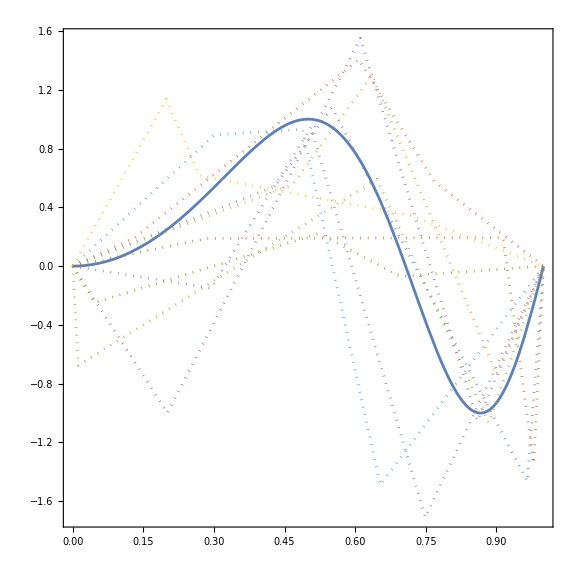

```mathematica
Show[ParametricPlot[{t,Sin[2π t^2]},{t,0,1},Frame->True,PlotRange->All,AspectRatio->1],
ListLinePlot[Map[First,Take[testdists,10]],
ImageSize->Large,Frame->True,PlotRange->All,PlotStyle->Dotted]]
```

```mathematica
filterbounds[bump_,limitfirst_,limitlast_,eps_:0.5]:=Module[{newbump},
newbump=bump;
newbump[[1]][[1]]=Max[bump[[1]][[1]],eps*limitfirst];
newbump[[-1]][[1]]=Min[bump[[-1]][[1]],eps*limitlast];
newbump
]
```

```mathematica
mutate[pts_,σ_,copies_,eps_:0.5]:=Module[{first,mid,last,limitfirst,limitlast,bumps,newmid},
first=First[pts];
last=Last[pts];
mid=Rest[Most[pts]];
limitfirst=first[[1]]-First[mid][[1]];
limitlast=last[[1]]-Last[mid][[1]];
bumps=Table[RandomVariate[NormalDistribution[0,σ],Dimensions[mid]],{copies}];
bumps=Map[filterbounds[#,limitfirst,limitlast,eps]&,bumps];
newmid=Map[(mid+#)&,bumps];
Map[Prepend[Append[#,last],first]&,newmid]];
```

```mathematica
mutate[pts4,0.025,5,0.5]
```

{{{0,0},{0.10757,0.0684503},{0.518315,1.14264},{0.512876,1.17425},{0.918508,-1.19683},{1.00001,-1.04067×10^-8}},{{0,0},{0.0923603,0.0571713},{0.526765,1.11199},{0.517433,1.10991},{0.91863,-1.2178},{1.00001,-1.04067×10^-8}},{{0,0},{0.117398,0.0604082},{0.493991,1.1329},{0.522461,1.12058},{0.856043,-1.15573},{1.00001,-1.04067×10^-8}},{{0,0},{0.0972345,0.0981018},{0.539948,1.08063},{0.514067,1.1054},{0.902425,-1.21375},{1.00001,-1.04067×10^-8}},{{0,0},{0.138687,0.0542298},{0.514117,1.11184},{0.533117,1.11123},{0.873909,-1.18253},{1.00001,-1.04067×10^-8}}}

```mathematica
next[sortedtbl_,best_,f_,T_,step_,rangex_,rangey_,n_,first_,last_,σ_,copies_,eps_:0.5]:=Module[{elite,mutations,newgen,all,ans},
elite=First[Transpose[Take[sortedtbl,best]]];
mutations=Flatten[Map[mutate[#,σ,copies,eps]&,elite],1];
newgen=Map[First,genpts[f,T,step,rangex,rangey,n,Length[sortedtbl]-Length[elite]-Length[mutations],first,last]];
all=Join[elite,mutations,newgen];
ans=SortBy[Map[{#,meandist[f,#,T,step]}&,all],Last];
ans
];
```

```mathematica
Take[testdists,10]
```

{{{{0,0},{0.428483,0.541832},{0.550594,1.07831},{0.965662,-1.46485},{1,0}},0.176679},{{{0,0},{0.466238,0.551874},{0.635532,1.29968},{0.900084,-0.736322},{1,0}},0.321025},{{{0,0},{0.0116157,-0.675311},{0.646102,0.590891},{0.88356,-1.06707},{1,0}},0.425471},{{{0,0},{0.131529,0.194279},{0.607465,1.40545},{0.767862,0.576229},{1,0}},0.447114},{{{0,0},{0.293655,-0.1499},{0.50605,0.944464},{0.74869,-1.71027},{1,0}},0.469485},{{{0,0},{0.283042,0.187902},{0.914062,0.194417},{0.97919,-1.3443},{1,0}},0.486424},{{{0,0},{0.300654,0.89224},{0.487948,0.930667},{0.653115,-1.48975},{1,0}},0.495588},{{{0,0},{0.1985,1.13487},{0.269125,0.61444},{0.717702,0.345607},{1,0}},0.500295},{{{0,0},{0.201105,-0.999416},{0.610929,1.54981},{0.859825,-1.05293},{1,0}},0.512805},{{{0,0},{0.0461939,-0.248717},{0.523389,0.22224},{0.695094,-0.0690825},{1,0}},0.532221}}

```mathematica
Timing[poplist=NestList[next[#,10,Sin[2π t^2],1,10^-3,{0,1},{-2,+2},3,{0,0},{1,0},0.025,4,0.5]&,testdists,100];]
```

{553.539,Null}

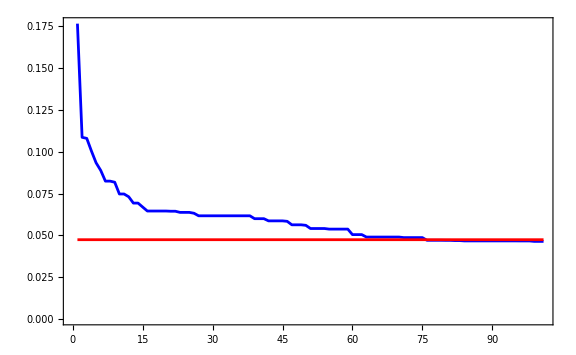

```mathematica
Show[ListLinePlot[Map[Last[First[#]]&,poplist],
Frame->True,PlotRange->All,ImageSize->Large,PlotStyle->Blue],
Plot[mfdsig4,{t,1,Length[poplist]},PlotStyle->Red]]
```

```mathematica
Take[Last[poplist],5]
```

{{{{0,0},{0.120333,0.071322},{0.546056,1.20162},{0.872586,-1.25094},{1,0}},0.0463897},{{{0,0},{0.152135,0.107427},{0.535123,1.22551},{0.876135,-1.23853},{1,0}},0.0464005},{{{0,0},{0.128247,0.0571393},{0.54585,1.18399},{0.877952,-1.25381},{1,0}},0.0466561},{{{0,0},{0.116169,0.0687639},{0.548309,1.1811},{0.874335,-1.23924},{1,0}},0.0466802},{{{0,0},{0.161356,0.149152},{0.537068,1.17552},{0.877066,-1.23964},{1,0}},0.0467674}}

```mathematica
pts4
```

{{0,0},{0.124866,0.0686851},{0.509697,1.10055},{0.530235,1.15509},{0.880021,-1.20377},{1.00001,-1.04067×10^-8}}

```mathematica
mfdsig4
```

0.0474057

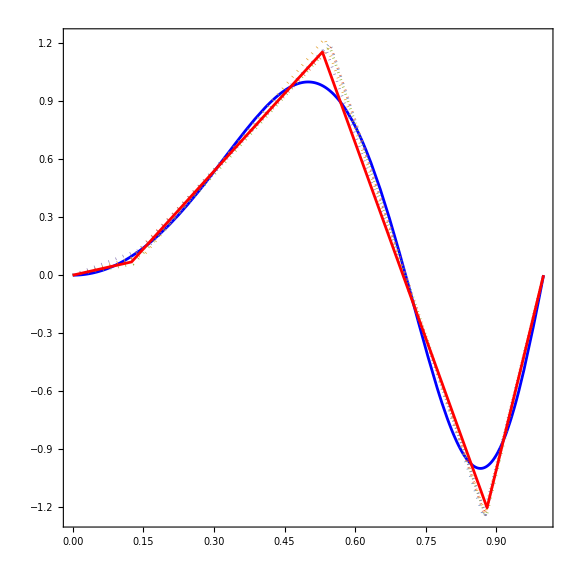

```mathematica
Show[ParametricPlot[{t,Sin[2π t^2]},{t,0,1},
Frame->True,PlotRange->All,AspectRatio->1,
ImageSize->Large,PlotStyle->Blue],
ListLinePlot[Take[Map[First,Last[poplist]],5],
PlotStyle->Dotted],
ListLinePlot[pts4,PlotStyle->Red]]
```

```mathematica
testdists[[1]]
```

{{{0,0},{0.428483,0.541832},{0.550594,1.07831},{0.965662,-1.46485},{1,0}},0.176679}